Datos salida\quadavg_linear_accel_TEK8_output.csv

FittedModel[…]

| Estimate | Standard Error | t-Statistic | P-Value
RPMs | 661.015 | 1.52379 | 433.795 | 2.291×10^-196

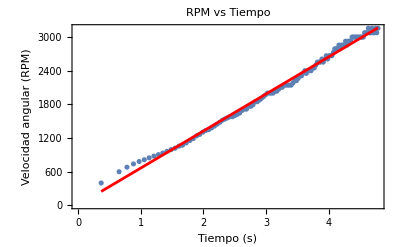

```mathematica
notebookDirectory = NotebookDirectory[];
fileName = "Datos salida\\quadavg_linear_accel_TEK8_output.csv"
fullPath = StringJoin[{notebookDirectory, fileName}];

data = Import[fullPath, "Data"];
data = data[[2;;]];
timeRPM = Transpose[{data[[All, 1]], data[[All, 3]]}];
dataPlot = ListPlot[timeRPM];

(*y-intercept is set zero.*)
fitModel = NonlinearModelFit[timeRPM, RPMs x, RPMs, x]
fitModel["ParameterTable"]

modelPlot = Plot[fitModel[x], {x, Min[timeRPM[[All, 1]]], Max[timeRPM[[All, 1]]]}, PlotStyle->Red];

Show[dataPlot, modelPlot, PlotLabel->"RPM vs Tiempo", Frame->True, FrameLabel->{"Tiempo (s)", "Velocidad angular (RPM)"}]
```